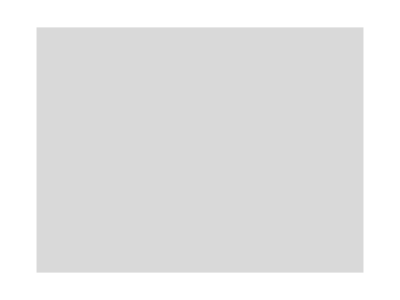

```mathematica
OpticSimulate[dim_, elem_] := Module[{canvas},
canvas = Rectangle[{-(dim[[1]])/2, -(dim[[2]])/2}, {(dim[[1]])/2, (dim[[2]])/2}];
Return[canvas]
]
Graphics[{LightGray, OpticSimulate[{4, 3}, {}]}]
```